# Globalna rast debelosti

## Pridobivanje podatkov

Podatke sem vzel iz Wolfram data repository.

```mathematica
ResourceData["Global Obesity Rates"]
```

## Pregled podatkov

Za lažji vpogled v podatke sem se odločil seznam urediti od najmanjše rasti do največije in obratno. Tako bom kasneje tudi primerjal med katerimi državami je bilo največ rasti in med katerimi najmanj.

```mathematica
TakeSmallestBy[ResourceData["Global Obesity Rates"],#Change&,5]
```

Opazimo da so vse države z najmanjšjo rastjo debelosti iz Azije.

```mathematica
najvecije = TakeLargestBy[ResourceData["Global Obesity Rates"],#Change&,5]
```

Države z največijo rastjoi debelosti so večinoma otočne države kar me je iskreno malo presenetilo.

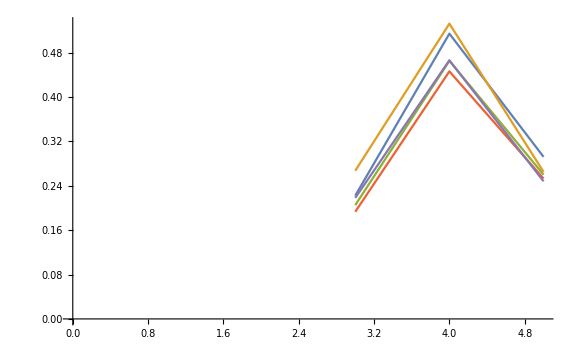

```mathematica
ListLinePlot[najvecije, ImageSize->Large]
```